```mathematica
(*
This notebook executes the computations needed to present the lift of the Deligne-Mostow lattice (5,4,1,1,1)/6 to the universal cover of SU(2,1).

The lift of the DM lattice to SU(2,1) will have generators b,u,v subject to the relations {b^3, u^3, v^6, b*v=v*b, u*b*u=b*u*b, (u*v)^2=(v*u)^2, (b*u*v)^3}.

Our lifts of these elements to the universal cover will be {B,U,V}.

The element of the universal cover of SU(2,1) mapping to a generator for the center <E^(2*Pi*I/3)*Id> of SU(2,1) will be denoted z.
Then z^3 is a generator for the universal cover of SU(2,1).

The presentation we find has relations
{B^3*z, U^3*z, V^6*z^-5, B*V=V*B, U*B*U=B*U*B, (U*V)^2=(V*U)^2, (B*U*V)^3}

One last remark is that we can replace V with W = Vz^-1, which changes the relations to{B^3*z, U^3*z, W^6*z, B*W=W*B, U*B*U=B*U*B, (U*W)^2=(W*U)^2, (B*U*W)^3*z^3}
This presentation fits into a more systematic picture for lifts of DM lattices.
*)
```

```mathematica
(* The standard hermitian form *)
h0 = {{0,0,1},{0,1,0},{1,0,0}};
```

```mathematica
(* The vector whose orbit is the our circle bundle over the ball *)
z0 = {-1,0,1};
```

```mathematica
(* Projection onto the third coordinate *)
p3 ={0,0,1};
```

```mathematica
(* Two matrix generators *)
x = {{1, 0, -1/Sqrt[-3]}, {0, E^(5*Pi*I/3), 0}, {Sqrt[-3], 0, 0}};
y = {{E^(5*Pi*I/3), E^(5*Pi*I/3), -1/Sqrt[-3]}, {Sqrt[-3], E^(2*Pi*I/3), 0}, {Sqrt[-3], 0, 0}};
```

```mathematica
(* The generators natural from realizing the quotient as P(1,2,3), normalized to have determinant one *)
b = (1/Det[x]^(1/3))*x//FullSimplify;
u = (1/Det[x]^(1/3))*y.x.Inverse[y]//FullSimplify;
v = (1/Det[y.Inverse[x.y.x].y]^(1/3))*y.Inverse[x.y.x].y//FullSimplify;
```

```mathematica
b//MatrixForm
```

((-1)^(1/9) | 0 | (-1)^(11/18)/(√3)
0 | -(-1)^(7/9) | 0
(-1)^(11/18) √3 | 0 | 0)

```mathematica
u//MatrixForm
```

(-(-1)^(7/9) | 0 | 0
(-1)^(11/18) √3 | (-1)^(4/9) | 0
(-1)^(11/18) √3 | (-1)^(11/18) √3 | -(-1)^(7/9))

```mathematica
v//MatrixForm
```

((-1)^(5/9) | 0 | 0
0 | (-1)^(8/9) | 0
0 | 0 | (-1)^(5/9))

```mathematica
Det[b]//FullSimplify
Det[u]//FullSimplify
Det[v]//FullSimplify
```

1

1

1

```mathematica
(* Checking that they preserve our hermitian form *)
Conjugate[Transpose[b]].h0.b-h0//FullSimplify
Conjugate[Transpose[u]].h0.u-h0//FullSimplify
Conjugate[Transpose[v]].h0.v-h0//FullSimplify
```

{{0,0,0},{0,0,0},{0,0,0}}

{{0,0,0},{0,0,0},{0,0,0}}

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
(* Power relations - they are all E^(4*Pi*I/3)*Id, a generator for the center of SU(2,1) *)
b.b.b-E^(4*Pi*I/3)*{{1,0,0},{0,1,0},{0,0,1}}//FullSimplify
u.u.u-E^(4*Pi*I/3)*{{1,0,0},{0,1,0},{0,0,1}}//FullSimplify
MatrixPower[v,6]-E^(4*Pi*I/3)*{{1,0,0},{0,1,0},{0,0,1}}//FullSimplify
```

{{0,0,0},{0,0,0},{0,0,0}}

{{0,0,0},{0,0,0},{0,0,0}}

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
(* Braid relations all lift to SU(2,1) *)
b.v-v.b//FullSimplify
u.b.u-b.u.b//FullSimplify
u.v.u.v-v.u.v.u//FullSimplify
```

{{0,0,0},{0,0,0},{0,0,0}}

{{0,0,0},{0,0,0},{0,0,0}}

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
(* Relation from the A_2 singularity lifts to SU(2,1) *)
MatrixPower[b.u.v,3]//FullSimplify
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
(* Matrix logarithm so we can define paths from Id to each generator *)
xb = MatrixLog[N[b,25]];
xu = MatrixLog[N[u,25]];
xv = MatrixLog[N[v,25]];
```

```mathematica
(* Remark: In the notation at the beginning of this document, z represents counterclockwise rotation by Pi/3, since z^3 generates the fundamental group of SU(2,1) *)
```

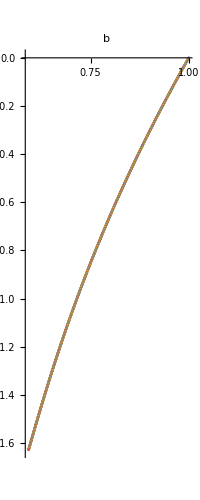

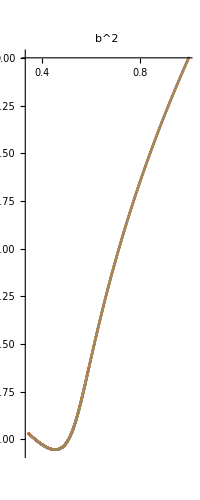

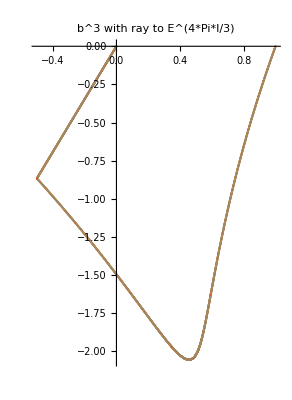

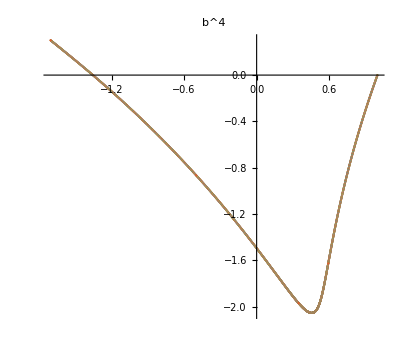

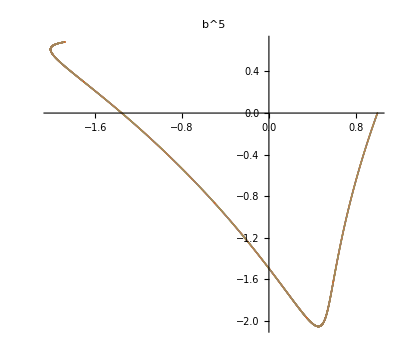

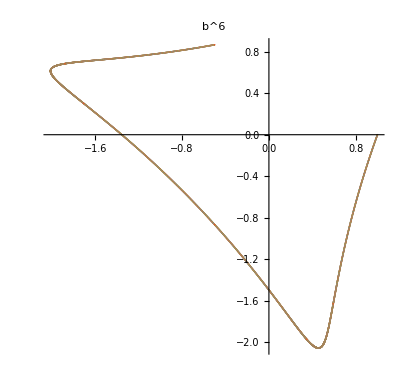

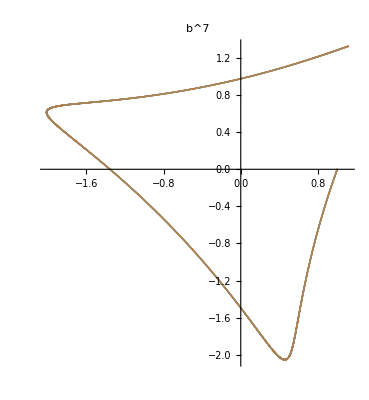

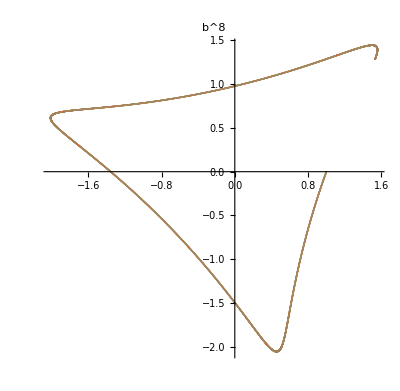

```mathematica
(* The relations b^3 central and b^9=Id for b turn clockwise, giving E^(4*Pi*I/3) at b^3, hence we lift to a relation B^3=z^-1, i.e., B^3*z *)
ListPlot[Table[{ReIm[(MatrixExp[s*xb].z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"b"]
ListPlot[Table[{ReIm[(MatrixExp[s*xb].z0).p3],ReIm[(MatrixExp[s*xb].b.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"b^2"]
ListPlot[Table[{ReIm[(MatrixExp[s*xb].z0).p3],ReIm[(MatrixExp[s*xb].b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.z0).p3],ReIm[s*E^(4*Pi*I/3)]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"b^3 with ray to E^(4*Pi*I/3)"]
ListPlot[Table[{ReIm[(MatrixExp[s*xb].z0).p3],ReIm[(MatrixExp[s*xb].b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"b^4"]
ListPlot[Table[{ReIm[(MatrixExp[s*xb].z0).p3],ReIm[(MatrixExp[s*xb].b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.b.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"b^5"]
ListPlot[Table[{ReIm[(MatrixExp[s*xb].z0).p3],ReIm[(MatrixExp[s*xb].b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.b.b.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"b^6"]
ListPlot[Table[{ReIm[(MatrixExp[s*xb].z0).p3],ReIm[(MatrixExp[s*xb].b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.b.b.b.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"b^7"]
ListPlot[Table[{ReIm[(MatrixExp[s*xb].z0).p3],ReIm[(MatrixExp[s*xb].b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.b.b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.b.b.b.b.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"b^8"]
ListPlot[Table[{ReIm[(MatrixExp[s*xb].z0).p3],ReIm[(MatrixExp[s*xb].b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.b.b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.b.b.b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.b.b.b.b.b.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"b^9 - full circle"]
```

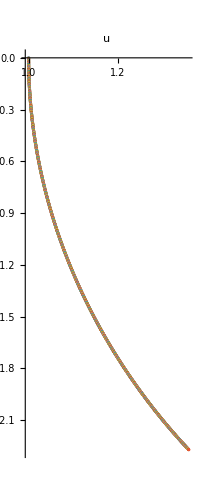

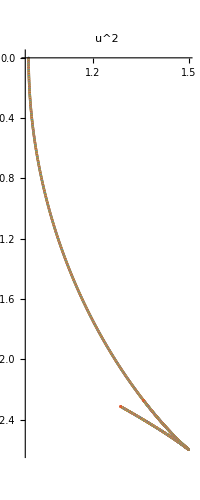

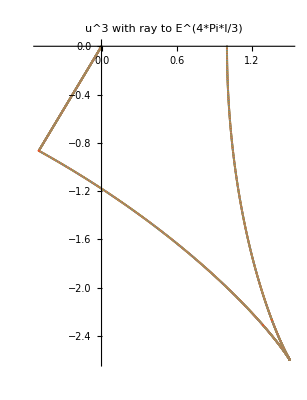

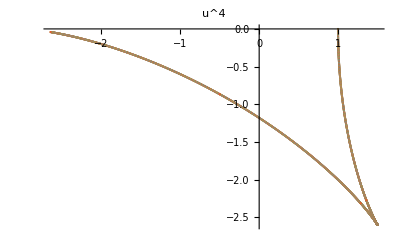

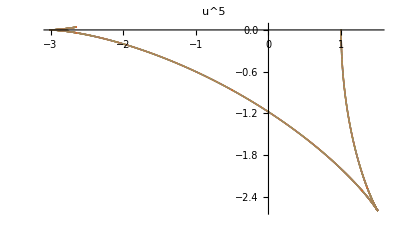

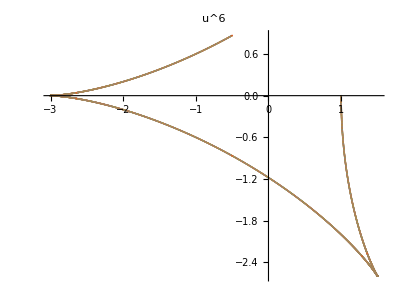

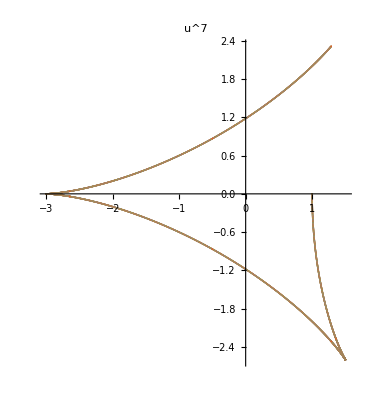

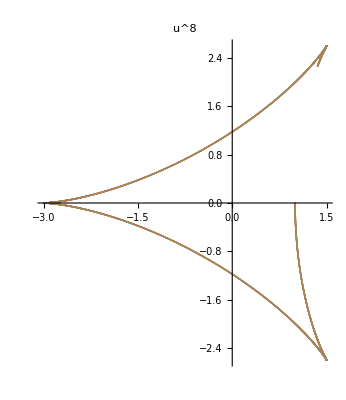

```mathematica
(* The relations u^3 central and u^9=Id for u turn clockwise, giving E^(4*Pi*I/3) at u^3, hence we lift to a relation U^3*z *)
ListPlot[Table[{ReIm[(MatrixExp[s*xu].z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"u"]
ListPlot[Table[{ReIm[(MatrixExp[s*xu].z0).p3],ReIm[(MatrixExp[s*xu].u.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"u^2"]
ListPlot[Table[{ReIm[(MatrixExp[s*xu].z0).p3],ReIm[(MatrixExp[s*xu].u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.z0).p3],ReIm[s*E^(4*Pi*I/3)]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"u^3 with ray to E^(4*Pi*I/3)"]
ListPlot[Table[{ReIm[(MatrixExp[s*xu].z0).p3],ReIm[(MatrixExp[s*xu].u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"u^4"]
ListPlot[Table[{ReIm[(MatrixExp[s*xu].z0).p3],ReIm[(MatrixExp[s*xu].u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.u.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"u^5"]
ListPlot[Table[{ReIm[(MatrixExp[s*xu].z0).p3],ReIm[(MatrixExp[s*xu].u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.u.u.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"u^6"]
ListPlot[Table[{ReIm[(MatrixExp[s*xu].z0).p3],ReIm[(MatrixExp[s*xu].u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.u.u.u.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"u^7"]
ListPlot[Table[{ReIm[(MatrixExp[s*xu].z0).p3],ReIm[(MatrixExp[s*xu].u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.u.u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.u.u.u.u.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"u^8"]
ListPlot[Table[{ReIm[(MatrixExp[s*xu].z0).p3],ReIm[(MatrixExp[s*xu].u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.u.u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.u.u.u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.u.u.u.u.u.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"u^9 - full circle"]
```

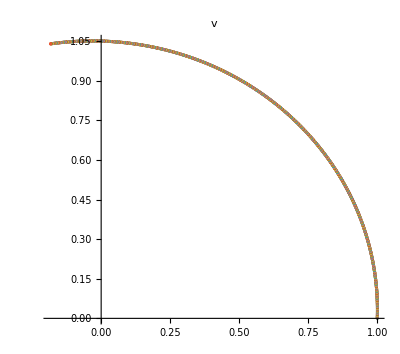

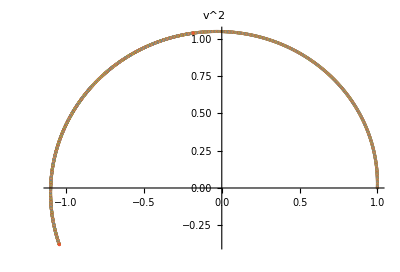

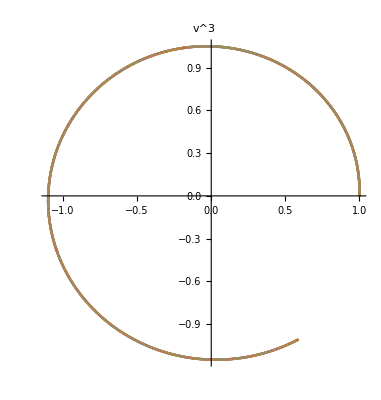

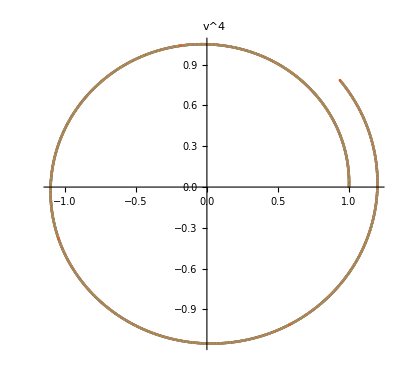

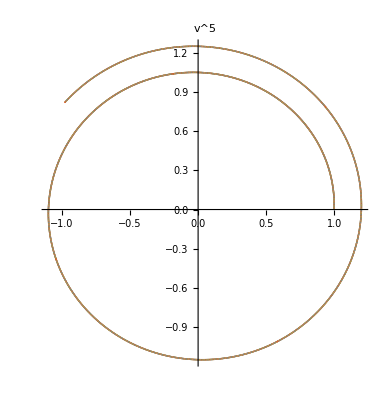

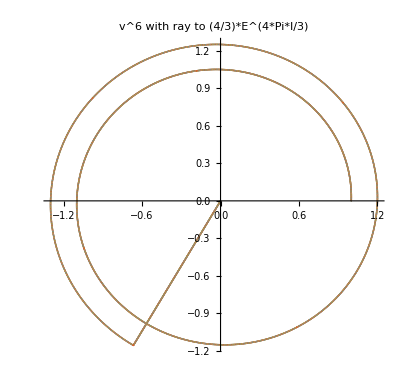

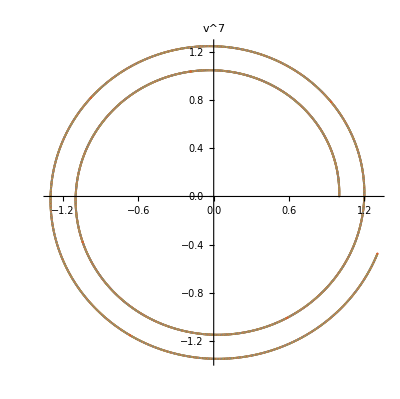

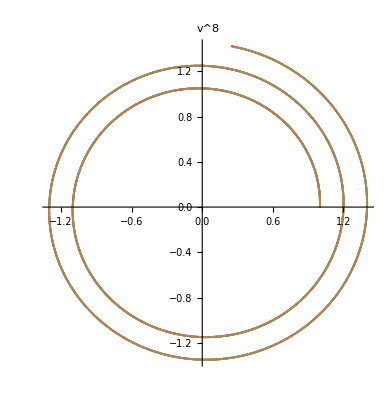

```mathematica
(* The relations v^6 central and v^18=Id for v turn counter-clockwise and wrap more than once - we increase the radius as we wrap to make this visible - and the lifted relation is therefore V^6*z^-5 *)
ListPlot[Table[{(1+s/18)*ReIm[(MatrixExp[s*xv].z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"v"]
ListPlot[Table[{(1+s/18)*ReIm[(MatrixExp[s*xv].z0).p3],(1+1/18+s/18)*ReIm[(MatrixExp[s*xv].v.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"v^2"]
ListPlot[Table[{(1+s/18)*ReIm[(MatrixExp[s*xv].z0).p3],(1+1/18+s/18)*ReIm[(MatrixExp[s*xv].v.z0).p3],(1+2/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"v^3"]
ListPlot[Table[{(1+s/18)*ReIm[(MatrixExp[s*xv].z0).p3],(1+1/18+s/18)*ReIm[(MatrixExp[s*xv].v.z0).p3],(1+2/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.z0).p3],(1+3/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"v^4"]
ListPlot[Table[{(1+s/18)*ReIm[(MatrixExp[s*xv].z0).p3],(1+1/18+s/18)*ReIm[(MatrixExp[s*xv].v.z0).p3],(1+2/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.z0).p3],(1+3/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.z0).p3],(1+4/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"v^5"]
ListPlot[Table[{(1+s/18)*ReIm[(MatrixExp[s*xv].z0).p3],(1+1/18+s/18)*ReIm[(MatrixExp[s*xv].v.z0).p3],(1+2/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.z0).p3],(1+3/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.z0).p3],(1+4/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.z0).p3],(1+5/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.z0).p3],ReIm[(4/3)*s*E^(4*Pi*I/3)]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"v^6 with ray to (4/3)*E^(4*Pi*I/3)"]
ListPlot[Table[{(1+s/18)*ReIm[(MatrixExp[s*xv].z0).p3],(1+1/18+s/18)*ReIm[(MatrixExp[s*xv].v.z0).p3],(1+2/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.z0).p3],(1+3/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.z0).p3],(1+4/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.z0).p3],(1+5/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.z0).p3],(1+6/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"v^7"]
ListPlot[Table[{(1+s/18)*ReIm[(MatrixExp[s*xv].z0).p3],(1+1/18+s/18)*ReIm[(MatrixExp[s*xv].v.z0).p3],(1+2/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.z0).p3],(1+3/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.z0).p3],(1+4/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.z0).p3],(1+5/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.z0).p3],(1+6/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.z0).p3],(1+7/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"v^8"]
ListPlot[Table[{(1+s/18)*ReIm[(MatrixExp[s*xv].z0).p3],(1+1/18+s/18)*ReIm[(MatrixExp[s*xv].v.z0).p3],(1+2/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.z0).p3],(1+3/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.z0).p3],(1+4/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.z0).p3],(1+5/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.z0).p3],(1+6/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.z0).p3],(1+7/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.z0).p3],(1+8/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"v^9"]
ListPlot[Table[{(1+s/18)*ReIm[(MatrixExp[s*xv].z0).p3],(1+1/18+s/18)*ReIm[(MatrixExp[s*xv].v.z0).p3],(1+2/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.z0).p3],(1+3/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.z0).p3],(1+4/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.z0).p3],(1+5/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.z0).p3],(1+6/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.z0).p3],(1+7/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.z0).p3],(1+8/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.z0).p3],(1+9/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"v^10"]
ListPlot[Table[{(1+s/18)*ReIm[(MatrixExp[s*xv].z0).p3],(1+1/18+s/18)*ReIm[(MatrixExp[s*xv].v.z0).p3],(1+2/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.z0).p3],(1+3/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.z0).p3],(1+4/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.z0).p3],(1+5/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.z0).p3],(1+6/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.z0).p3],(1+7/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.z0).p3],(1+8/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.z0).p3],(1+9/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.z0).p3],
(1+10/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.v.z0).p3]},
{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"v^11"]
ListPlot[Table[{(1+s/18)*ReIm[(MatrixExp[s*xv].z0).p3],(1+1/18+s/18)*ReIm[(MatrixExp[s*xv].v.z0).p3],(1+2/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.z0).p3],(1+3/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.z0).p3],(1+4/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.z0).p3],(1+5/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.z0).p3],(1+6/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.z0).p3],(1+7/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.z0).p3],(1+8/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.z0).p3],(1+9/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.z0).p3],
(1+10/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.v.z0).p3],
(1+11/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.v.v.z0).p3]},
{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"v^12"]
ListPlot[Table[{(1+s/18)*ReIm[(MatrixExp[s*xv].z0).p3],(1+1/18+s/18)*ReIm[(MatrixExp[s*xv].v.z0).p3],(1+2/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.z0).p3],(1+3/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.z0).p3],(1+4/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.z0).p3],(1+5/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.z0).p3],(1+6/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.z0).p3],(1+7/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.z0).p3],(1+8/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.z0).p3],(1+9/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.z0).p3],
(1+10/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.v.z0).p3],
(1+11/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.v.v.z0).p3],(1+12/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.v.v.v.z0).p3]},
{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"v^13"]
ListPlot[Table[{(1+s/18)*ReIm[(MatrixExp[s*xv].z0).p3],(1+1/18+s/18)*ReIm[(MatrixExp[s*xv].v.z0).p3],(1+2/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.z0).p3],(1+3/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.z0).p3],(1+4/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.z0).p3],(1+5/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.z0).p3],(1+6/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.z0).p3],(1+7/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.z0).p3],(1+8/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.z0).p3],(1+9/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.z0).p3],
(1+10/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.v.z0).p3],
(1+11/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.v.v.z0).p3],(1+12/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.v.v.v.z0).p3],(1+13/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.v.v.v.v.z0).p3]},
{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"v^14"]
ListPlot[Table[{(1+s/18)*ReIm[(MatrixExp[s*xv].z0).p3],(1+1/18+s/18)*ReIm[(MatrixExp[s*xv].v.z0).p3],(1+2/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.z0).p3],(1+3/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.z0).p3],(1+4/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.z0).p3],(1+5/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.z0).p3],(1+6/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.z0).p3],(1+7/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.z0).p3],(1+8/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.z0).p3],(1+9/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.z0).p3],
(1+10/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.v.z0).p3],
(1+11/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.v.v.z0).p3],(1+12/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.v.v.v.z0).p3],(1+13/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.v.v.v.v.z0).p3],(1+14/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.v.v.v.v.v.z0).p3]},
{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"v^15"]
ListPlot[Table[{(1+s/18)*ReIm[(MatrixExp[s*xv].z0).p3],(1+1/18+s/18)*ReIm[(MatrixExp[s*xv].v.z0).p3],(1+2/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.z0).p3],(1+3/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.z0).p3],(1+4/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.z0).p3],(1+5/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.z0).p3],(1+6/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.z0).p3],(1+7/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.z0).p3],(1+8/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.z0).p3],(1+9/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.z0).p3],
(1+10/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.v.z0).p3],
(1+11/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.v.v.z0).p3],(1+12/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.v.v.v.z0).p3],(1+13/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.v.v.v.v.z0).p3],(1+14/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.v.v.v.v.v.z0).p3],(1+15/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.v.v.v.v.v.v.z0).p3]},
{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"v^16"]
ListPlot[Table[{(1+s/18)*ReIm[(MatrixExp[s*xv].z0).p3],(1+1/18+s/18)*ReIm[(MatrixExp[s*xv].v.z0).p3],(1+2/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.z0).p3],(1+3/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.z0).p3],(1+4/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.z0).p3],(1+5/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.z0).p3],(1+6/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.z0).p3],(1+7/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.z0).p3],(1+8/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.z0).p3],(1+9/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.z0).p3],
(1+10/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.v.z0).p3],
(1+11/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.v.v.z0).p3],(1+12/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.v.v.v.z0).p3],(1+13/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.v.v.v.v.z0).p3],(1+14/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.v.v.v.v.v.z0).p3],(1+15/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.v.v.v.v.v.v.z0).p3],(1+16/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.v.v.v.v.v.v.v.z0).p3]},
{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"v^17"]
ListPlot[Table[{(1+s/18)*ReIm[(MatrixExp[s*xv].z0).p3],(1+1/18+s/18)*ReIm[(MatrixExp[s*xv].v.z0).p3],(1+2/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.z0).p3],(1+3/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.z0).p3],(1+4/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.z0).p3],(1+5/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.z0).p3],(1+6/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.z0).p3],(1+7/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.z0).p3],(1+8/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.z0).p3],(1+9/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.z0).p3],
(1+10/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.v.z0).p3],
(1+11/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.v.v.z0).p3],(1+12/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.v.v.v.z0).p3],(1+13/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.v.v.v.v.z0).p3],(1+14/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.v.v.v.v.v.z0).p3],(1+15/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.v.v.v.v.v.v.z0).p3],(1+16/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.v.v.v.v.v.v.v.z0).p3],(1+17/18+s/18)*ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.v.v.v.v.v.v.v.v.z0).p3]},
{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"v^18 with five full rotations"]
```

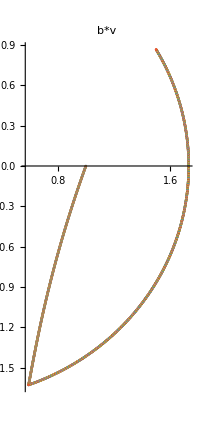

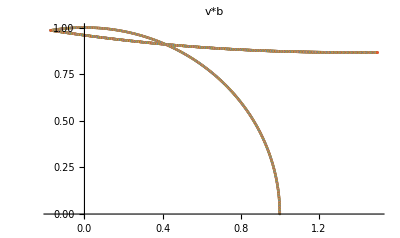

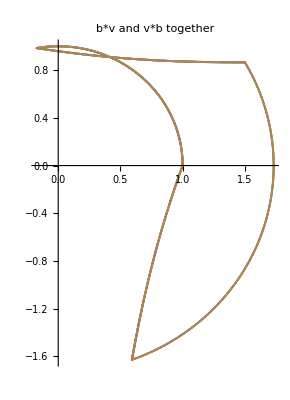

```mathematica
(* The relation b*v=v*b lifts to the universal cover, since the combined loop is nullhomotopic in C-{0} *)
ListPlot[Table[{ReIm[(MatrixExp[s*xb].z0).p3],ReIm[(MatrixExp[s*xv].b.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"b*v"]
ListPlot[Table[{ReIm[(MatrixExp[s*xv].z0).p3],ReIm[(MatrixExp[s*xb].v.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"v*b"]
ListPlot[Table[{ReIm[(MatrixExp[s*xb].z0).p3],ReIm[(MatrixExp[s*xv].b.z0).p3],ReIm[(MatrixExp[s*xv].z0).p3],ReIm[(MatrixExp[s*xb].v.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"b*v and v*b together"]
```

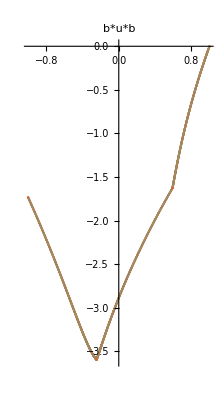

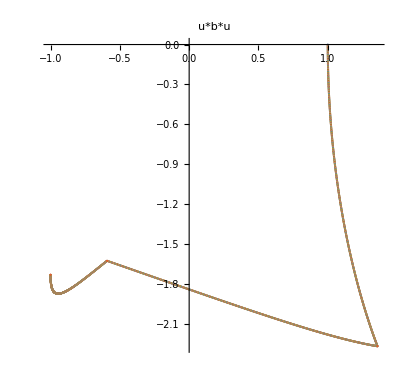

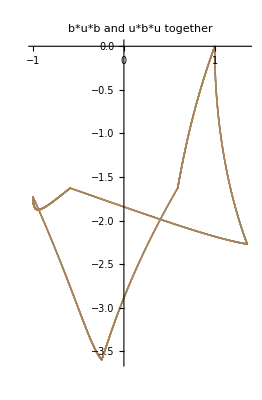

```mathematica
(* The relation b*u*b=u*b*u lifts to the universal cover, since the combined loop is nullhomotopic in C-{0} *)
ListPlot[Table[{ReIm[(MatrixExp[s*xb].z0).p3],ReIm[(MatrixExp[s*xu].b.z0).p3],ReIm[(MatrixExp[s*xb].u.b.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"b*u*b"]
ListPlot[Table[{ReIm[(MatrixExp[s*xu].z0).p3],ReIm[(MatrixExp[s*xb].u.z0).p3],ReIm[(MatrixExp[s*xu].b.u.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"u*b*u"]
ListPlot[Table[{ReIm[(MatrixExp[s*xb].z0).p3],ReIm[(MatrixExp[s*xu].b.z0).p3],ReIm[(MatrixExp[s*xb].u.b.z0).p3],ReIm[(MatrixExp[s*xu].z0).p3],ReIm[(MatrixExp[s*xb].u.z0).p3],ReIm[(MatrixExp[s*xu].b.u.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"b*u*b and u*b*u together"]
```

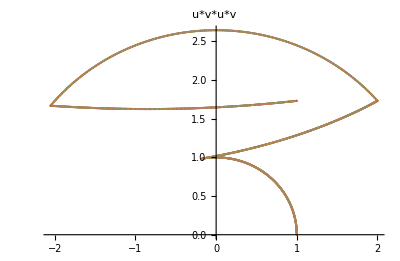

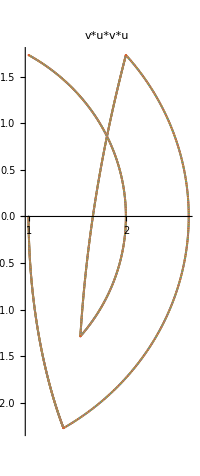

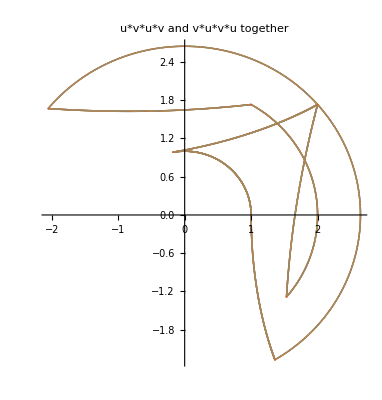

```mathematica
(* The relation u*v*u*v=v*u*v*ulifts to the universal cover, since the combined loop is nullhomotopic in C-{0} *)
ListPlot[Table[{ReIm[(MatrixExp[s*xv].z0).p3],ReIm[(MatrixExp[s*xu].v.z0).p3],ReIm[(MatrixExp[s*xv].u.v.z0).p3],ReIm[(MatrixExp[s*xu].v.u.v.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"u*v*u*v"]
ListPlot[Table[{ReIm[(MatrixExp[s*xu].z0).p3],ReIm[(MatrixExp[s*xv].u.z0).p3],ReIm[(MatrixExp[s*xu].v.u.z0).p3],ReIm[(MatrixExp[s*xv].u.v.u.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"v*u*v*u"]
ListPlot[Table[{ReIm[(MatrixExp[s*xv].z0).p3],ReIm[(MatrixExp[s*xu].v.z0).p3],ReIm[(MatrixExp[s*xv].u.v.z0).p3],ReIm[(MatrixExp[s*xu].v.u.v.z0).p3],ReIm[(MatrixExp[s*xu].z0).p3],ReIm[(MatrixExp[s*xv].u.z0).p3],ReIm[(MatrixExp[s*xu].v.u.z0).p3],ReIm[(MatrixExp[s*xv].u.v.u.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"u*v*u*v and v*u*v*u together"]
```

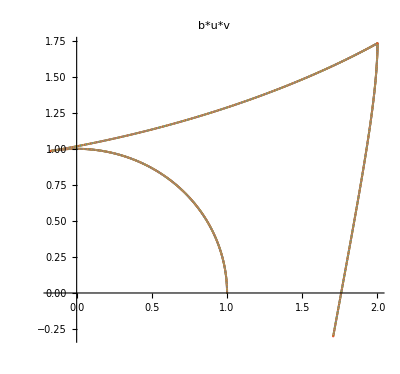

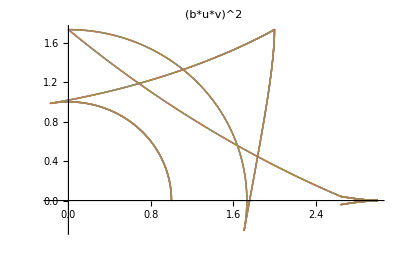

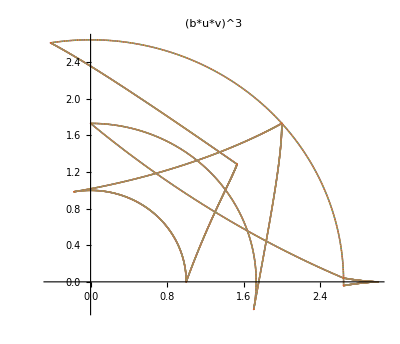

```mathematica
(* The relation (b*u*v)^3=Id lifts to the universal cover *)
ListPlot[Table[{ReIm[(MatrixExp[s*xv].z0).p3],ReIm[(MatrixExp[s*xu].v.z0).p3],ReIm[(MatrixExp[s*xb].u.v.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"b*u*v"]
ListPlot[Table[{ReIm[(MatrixExp[s*xv].z0).p3],ReIm[(MatrixExp[s*xu].v.z0).p3],ReIm[(MatrixExp[s*xb].u.v.z0).p3],ReIm[(MatrixExp[s*xv].b.u.v.z0).p3],ReIm[(MatrixExp[s*xu].v.b.u.v.z0).p3],ReIm[(MatrixExp[s*xb].u.v.b.u.v.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"(b*u*v)^2"]
ListPlot[Table[{ReIm[(MatrixExp[s*xv].z0).p3],ReIm[(MatrixExp[s*xu].v.z0).p3],ReIm[(MatrixExp[s*xb].u.v.z0).p3],ReIm[(MatrixExp[s*xv].b.u.v.z0).p3],ReIm[(MatrixExp[s*xu].v.b.u.v.z0).p3],ReIm[(MatrixExp[s*xb].u.v.b.u.v.z0).p3],ReIm[(MatrixExp[s*xv].b.u.v.b.u.v.z0).p3],ReIm[(MatrixExp[s*xu].v.b.u.v.b.u.v.z0).p3],ReIm[(MatrixExp[s*xb].u.v.b.u.v.b.u.v.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"(b*u*v)^3"]
```